# Markdown Parser Demo

Parse a markdown file to Symbolic Markdown

If you make any changes to either package, Quit the kernel

Quit the kernel

```mathematica
Quit
```

Install the packages again from the Menu:

File » Install » Source: » From File » MarkdownParse.wl

File » Install » Source: » From File » MarkdownParserTests.wl

Then load both packages

Load MarkdownParse` and MarkdownParserTests`

```mathematica
<<MarkdownParse`
<<MarkdownParserTests`
```

## MarkdownElements

Displayed below are supported MarkdownElements

```mathematica
Values[$MarkdownParsePrimitives]//Column[#,ItemStyle->{{"Code"}},Frame->All]&
```

MarkdownElement[H1,$2]
MarkdownElement[Bold,$2]
MarkdownElement[Italic,$2]
MarkdownElement[LaTeX,<|Type→Display,Body→$2|>]
MarkdownElement[LaTeX,<|Type→Display,Body→$3|>]
MarkdownElement[LaTeX,<|Type→Inline,Body→$2|>]
MarkdownElement[LaTeX,<|Type→Inline,Body→$3|>]
MarkdownElement[LaTeX,<|Type→Inline,Body→$3|>]
MarkdownElement[Hyperlink,<|Label→$1,Link→$2|>]
MarkdownElement[Hyperlink,<|Link→$1|>]
MarkdownElement[Hyperlink,<|AltText→$1,Link→$2|>]
MarkdownElement[Hyperlink,$1,MarkdownElement[FootnoteReference,{$2}]]
MarkdownElement[ItemNumbered,{$1},$2]
MarkdownElement[Item,<|IndentationLevel→1,IndentationType→Whitespace,Content→$2|>]
MarkdownElement[BlockQuote,$1]
MarkdownElement[CodeBlock,<|Language→$2,Body→$3|>]
MarkdownElement[CodeBlock,<|Language→None,Body→$2|>]
MarkdownElement[CodeBlock,<|Language→None,Body→$1|>]
MarkdownElement[InlineCode,$2]
MarkdownElement[HorizontalLine]

## MarkdownParse Example

```mathematica
filePath=FileNameJoin[{NotebookDirectory[],"test.md"}];
```

```mathematica
Import[filePath,"String"]
```

# An exhibit of Markdown

This note demonstrates some of what [Markdown][1] is capable of doing.

_Note: Feel free to play with this page. Unlike regular notes, this doesn't automatically save itself._

## Basic formatting

Write Paragraphs like so. A paragraph is the basic block of Markdown. A paragraph is what text will turn into when there is no reason it should become anything else.

Blank lines separate paragraphs. Markdown supports _italic_ and **bold** formatting.

Lines can have nested styling as well, like _a **bold** in an italic_.

## Lists

### Ordered list

1. Item 1
2. A second item
3. Number 3
4. â.85£

_Note: the fourth item uses the Unicode character for [Roman numeral four][2]._

### Unordered list

* An item
* Another item
* Yet another item
* And there's more...

## Paragraph modifiers

### Code block

    Code blocks are useful for people who look at code or for clarity of plain text content. As you can see, it uses a fixed-width font.

You can also make `inline code` to add insert code block formatting anywhere.

### Quote

> Here is a quote. What this is should be self explanatory. Quotes are automatically indented when they are used.

## Headings

Markdown supports six levels of headings; corresponding with the six levels of HTML headings. You've probably noticed them already in the page. Each level down uses one more hash character.

### Headings _can_ also contain **formatting**

### They can even contain `inline code`

Of course, demonstrating what headings look like messes up the structure of the page.

I don't recommend using more than three or four levels of headings here, because, when you're smallest heading isn't too small, and you're largest heading isn't too big, and you want each size up to look noticeably larger and more important, there aren't any other sizes to choose from.

## LaTex

LaTex is also supported:

* inline

\(a^2 + b^2 = c^2\)

$ a^2 + b^2 = c^2 $

* presented

\[ a^n + b^n = c^n \]

$$ a^2 + b^2 = c^2 $$


## URLs

Add hyperlinks in the following ways:

* A named link to [MarkItDown][3]. The easiest way to do these is to select what you want to make a link and hit `Ctrl+L`.
* Another named link to [MarkItDown](http://www.markitdown.net/)
* Sometimes you want the URL : <http://www.markitdown.net/>.

## Horizontal rule

A horizontal rule is a dividing line drawn across the page, useful for separating blocks of text.

---

## Tables

Markdown | Less | Pretty
--- | --- | ---
*Still* | `renders` | **nicely**
1 | 2 | 3

## Images

Markdown can also contain images.
![Streetview of Palm Trees by Brandon Erlinger-Ford](https://images.unsplash.com/photo-1564889998041-0dacc0706a0f?ixid=MXwxMjA3fDB8MHxwaG90by1wYWdlfHx8fGVufDB8fHw%3D&ixlib=rb-1.2.1&auto=format&fit=crop&w=564&q=80)

## Last

There's actually a lot more to Markdown than this. See the official [introduction][4] and [syntax][5] for more information. Be aware that this document is not using the official implementation, and there may be subtle differences in rendering on other platforms.


  [1]: http://daringfireball.net/projects/markdown/
  [2]: http://www.fileformat.info/info/unicode/char/2163/index.htm
  [3]: http://www.markitdown.net/
  [4]: http://daringfireball.net/projects/markdown/basics
  [5]: http://daringfireball.net/projects/markdown/syntax

```mathematica
mdp=MarkdownParse[filePath];
```

```mathematica
Column[mdp,Frame->All]
```

MarkdownElement[H1,An exhibit of Markdown]
{This note demonstrates some of what,MarkdownElement[Hyperlink,Markdown, http://daringfireball.net/projects/markdown/], is capable of doing.}
MarkdownElement[Italic,Note: Feel free to play with this page. Unlike regular notes, this doesn't automatically save itself.]
MarkdownElement[H2,Basic formatting]
Write Paragraphs like so. A paragraph is the basic block of Markdown. A paragraph is what text will turn into when there is no reason it should become anything else.
{Blank lines separate paragraphs. Markdown supports ,MarkdownElement[Italic,italic], and ,MarkdownElement[Bold,bold], formatting.}
{Lines can have nested styling as well, like ,MarkdownElement[Italic,{a ,MarkdownElement[Bold,bold], in an italic}],.}
MarkdownElement[H2,Lists]
MarkdownElement[H3,Ordered list]
MarkdownElement[ItemNumbered,{1},Item 1]
MarkdownElement[ItemNumbered,{2},A second item]
MarkdownElement[ItemNumbered,{3},Number 3]
MarkdownElement[ItemNumbered,{4},Ⅳ]
MarkdownElement[Italic,{Note: the fourth item uses the Unicode character for,MarkdownElement[Hyperlink,Roman numeral four, http://www.fileformat.info/info/unicode/char/2163/index.htm],.}]
MarkdownElement[H3,Unordered list]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→An item|>]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→Another item|>]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→Yet another item|>]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→And there's more...|>]
MarkdownElement[H2,Paragraph modifiers]
MarkdownElement[H3,Code block]
MarkdownElement[CodeBlock,<|Language→None,Body→Code blocks are useful for people who look at code or for clarity of plain text content. As you can see, it uses a fixed-width font.|>]
{You can also make ,MarkdownElement[InlineCode,inline code], to add insert code block formatting anywhere.}
MarkdownElement[H3,Quote]
MarkdownElement[BlockQuote,Here is a quote. What this is should be self explanatory. Quotes are automatically indented when they are used.]
MarkdownElement[H2,Headings]
Markdown supports six levels of headings; corresponding with the six levels of HTML headings. You've probably noticed them already in the page. Each level down uses one more hash character.
MarkdownElement[H3,{Headings ,MarkdownElement[Italic,can], also contain ,MarkdownElement[Bold,formatting]}]
MarkdownElement[H3,{They can even contain ,MarkdownElement[InlineCode,inline code]}]
Of course, demonstrating what headings look like messes up the structure of the page.
I don't recommend using more than three or four levels of headings here, because, when you're smallest heading isn't too small, and you're largest heading isn't too big, and you want each size up to look noticeably larger and more important, there aren't any other sizes to choose from.
MarkdownElement[H2,LaTex]
LaTex is also supported:
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→inline|>]
MarkdownElement[LaTeX,<|Type→Inline,Body→a^2 + b^2 = c^2|>]
MarkdownElement[LaTeX,<|Type→Inline,Body→ a^2 + b^2 = c^2 |>]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→presented|>]
MarkdownElement[LaTeX,<|Type→Display,Body→a^n + b^n = c^n|>]
MarkdownElement[LaTeX,<|Type→Display,Body→ a^2 + b^2 = c^2 |>]
MarkdownElement[H2,URLs]
Add hyperlinks in the following ways:
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→{A named link to,MarkdownElement[Hyperlink,MarkItDown,First[Private`ExtractMarkdownFootnoteURL[3,Private`footFile]]],. The easiest way to do these is to select what you want to make a link and hit ,MarkdownElement[InlineCode,Ctrl+L],.}|>]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→{Another named link to,MarkdownElement[Hyperlink,<|Label→MarkItDown,Link→http://www.markitdown.net/|>]}|>]
MarkdownElement[Item,<|IndentationLevel→0,IndentationType→None,Content→{Sometimes you want the URL : ,MarkdownElement[Hyperlink,<|Link→http://www.markitdown.net/|>],.}|>]
MarkdownElement[H2,Horizontal rule]
A horizontal rule is a dividing line drawn across the page, useful for separating blocks of text.
MarkdownElement[HorizontalLine]
MarkdownElement[H2,Tables]
MarkdownElement[Table,{MarkdownElement[TableHeader,{Markdown , Less , Pretty}],MarkdownElement[TableAlignment,{{Center},{Center},{Center}}],{MarkdownElement[TableRow,{{MarkdownElement[Italic,Still], },{ ,MarkdownElement[InlineCode,renders], },{ ,MarkdownElement[Bold,nicely]}}],MarkdownElement[TableRow,{1 , 2 , 3}]}}]
MarkdownElement[H2,Images]
Markdown can also contain images.
MarkdownElement[Hyperlink,<|AltText→Streetview of Palm Trees by Brandon Erlinger-Ford,Link→https://images.unsplash.com/photo-1564889998041-0dacc0706a0f?ixid=MXwxMjA3fDB8MHxwaG90by1wYWdlfHx8fGVufDB8fHw%3D&ixlib=rb-1.2.1&auto=format&fit=crop&w=564&q=80|>]
MarkdownElement[H2,Last]
{There's actually a lot more to Markdown than this. See the official,MarkdownElement[Hyperlink,introduction, http://daringfireball.net/projects/markdown/basics], and,MarkdownElement[Hyperlink,syntax, http://daringfireball.net/projects/markdown/syntax], for more information. Be aware that this document is not using the official implementation, and there may be subtle differences in rendering on other platforms.}

Not sure why ExtractMarkdownFootnote doesn’t work ↓↓↓

```mathematica
MarkdownElement["Item",<|"IndentationLevel"->0,"IndentationType"->None,"Content"->{"A named link to",MarkdownElement[Hyperlink,"MarkItDown",First[Private`ExtractMarkdownFootnoteURL[3,Private`footFile]]],". The easiest way to do these is to select what you want to make a link and hit ",MarkdownElement["InlineCode","Ctrl+L"],"."}|>]
```

## TestParser

```mathematica
MarkdownParserTestReport
```

TestReportObject[…]

## Markdown Graphs

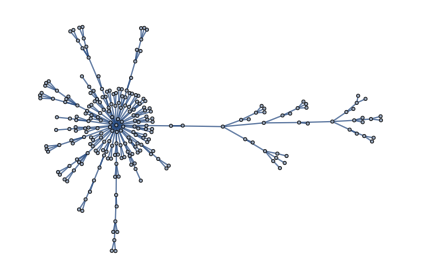

```mathematica
ExpressionGraph[mdp,VertexLabels->Placed[Automatic,Tooltip]]
```